```mathematica
RandomSample[Join[Flatten[Table[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10},5]],Flatten[Table[{imp11,imp12,imp13,imp14},1]],Flatten[Table[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8},5]],Table[imp,6]]]
```

{imp2,imp10,imp8,imp9,imp8,imp6,imp,imp3,imp6,imp7,imp1,imp7,imp13,imp14,imp2,imp1,imp3,imp4,imp,imp4,imp,imp4,imp7,imp4,imp,imp5,imp7,imp6,imp6,imp7,imp10,imp5,imp3,imp4,imp3,imp3,imp1,imp6,imp9,imp10,imp4,imp,imp3,imp2,imp2,imp4,imp1,imp7,imp2,imp9,imp2,imp3,imp1,imp8,imp5,imp8,imp2,imp7,imp6,imp5,imp9,imp12,imp7,imp5,imp1,imp10,imp2,imp3,imp1,imp8,imp7,imp4,imp6,imp8,imp8,imp2,imp6,imp8,imp11,imp3,imp4,imp2,imp8,imp1,imp4,imp10,imp6,imp6,imp1,imp5,imp5,imp,imp5,imp5,imp8,imp9,imp1,imp5,imp7,imp3}

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
Leads=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,0.-1464.47 ⅈ,-0.176777+0. ⅈ,0.+1035.53 ⅈ,0.0732233+0. ⅈ,0.-1,0.0303301+0. ⅈ,0.+428.932 ⅈ,0.103553+0. ⅈ,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Leads[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SL[ω,δ,t,ϵ,m]=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=ParallelTable[{ω,tr[ω,0.0001,1,0,7]},{ω,Range[0,3,0.01]}]//AbsoluteTiming
```

{3.79277,{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}}

```mathematica
l1={{2,12,14},{4,10,12},{6,10,8},{2,4,12},{4,6,10}}
```

{{2,12,14},{4,10,12},{6,10,8},{2,4,12},{4,6,10}}

```mathematica
l={{1,3,13},{3,13,11},{3,5,13},{5,7,9},{11,9,5}}
```

{{1,3,13},{3,13,11},{3,5,13},{5,7,9},{11,9,5}}

```mathematica
m1[ω_,ϵ1_]:=Block[{Tin=T1[1,7],T=ρ[1,7],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}],a1=RandomSample[Flatten[RandomSample[l,1]],2],a2=RandomSample[Flatten[RandomSample[l,1]],2],a3=RandomSample[Flatten[RandomSample[l1,1]],2],a4=RandomSample[Flatten[RandomSample[l1,1]],2]},
imp1:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];imp9:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a1[[1]],a1[[1]]},{a1[[2]],a1[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a2[[1]],a2[[1]]},{a2[[2]],a2[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a3[[1]],a3[[1]]},{a3[[2]],a3[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a4[[1]],a4[[1]]},{a4[[2]],a4[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra1:=Block[{J=SL[ω,0.0001,1,0,7]},
b=Block[{},
lista={RandomSample[{imp2,imp10,imp8,imp9,imp8,imp6,imp,imp3,imp6,imp7,imp1,imp7,imp13,imp14,imp2,imp1,imp3,imp4,imp,imp4,imp,imp4,imp7,imp4,imp,imp5,imp7,imp6,imp6,imp7,imp10,imp5,imp3,imp4,imp3,imp3,imp1,imp6,imp9,imp10,imp4,imp,imp3,imp2,imp2,imp4,imp1,imp7,imp2,imp9,imp2,imp3,imp1,imp8,imp5,imp8,imp2,imp7,imp6,imp5,imp9,imp12,imp7,imp5,imp1,imp10,imp2,imp3,imp1,imp8,imp7,imp4,imp6,imp8,imp8,imp2,imp6,imp8,imp11,imp3,imp4,imp2,imp8,imp1,imp4,imp10,imp6,imp6,imp1,imp5,imp5,imp,imp5,imp5,imp8,imp9,imp1,imp5,imp7,imp3}]};
sl1= Block[{},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0,7],tr[ω,0.0001,1,0,7],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
tr1];
b];
tra1]
```

```mathematica
m1[1,1]
```

0.327992

```mathematica
m1pair4= Compile[{ω},m1[ω,0.5],CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True}]
```

CompiledFunction[…]

```mathematica
Mean[Table[m1pair4[1],2000]]//AbsoluteTiming
```

{47.2156,1.05819}

```mathematica
Table[{ω,Mean[ParallelTable[m1pair4[ω],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.8×10^-7},{0.01,2.80659×10^-7},{0.02,2.8251×10^-7},{0.03,2.84873×10^-7},{0.04,2.87361×10^-7},{0.05,2.899×10^-7},{0.06,2.93812×10^-7},{0.07,2.99557×10^-7},{0.08,3.06951×10^-7},{0.09,3.17275×10^-7},{0.1,3.30238×10^-7},{0.11,3.46255×10^-7},{0.12,3.66927×10^-7},{0.13,3.90083×10^-7},{0.14,4.23073×10^-7},{0.15,4.65342×10^-7},{0.16,5.12793×10^-7},{0.17,5.85854×10^-7},{0.18,6.83546×10^-7},{0.19,8.11042×10^-7},{0.2,1.03439×10^-6},{0.21,1.35983×10^-6},{0.22,1.92203×10^-6},{0.23,3.16118×10^-6},{0.24,7.68893×10^-6},{0.25,0.00437141},{0.26,0.0351783},{0.27,0.120184},{0.28,0.208231},{0.29,0.264102},{0.3,0.288933},{0.31,0.321391},{0.32,0.333817},{0.33,0.358081},{0.34,0.372371},{0.35,0.371508},{0.36,0.365266},{0.37,0.381622},{0.38,0.388816},{0.39,0.39557},{0.4,0.420304},{0.41,0.407333},{0.42,0.422068},{0.43,0.409298},{0.44,0.309526},{0.45,0.268708},{0.46,0.307277},{0.47,0.374391},{0.48,0.423336},{0.49,0.45563},{0.5,0.480186},{0.51,0.51873},{0.52,0.543067},{0.53,0.555505},{0.54,0.572137},{0.55,0.572816},{0.56,0.582799},{0.57,0.607556},{0.58,0.592873},{0.59,0.628651},{0.6,0.630428},{0.61,0.647868},{0.62,0.651887},{0.63,0.653542},{0.64,0.676188},{0.65,0.678392},{0.66,0.691945},{0.67,0.693048},{0.68,0.680908},{0.69,0.695609},{0.7,0.705563},{0.71,0.7355},{0.72,0.714199},{0.73,0.7191},{0.74,0.74819},{0.75,0.742791},{0.76,0.75995},{0.77,0.754603},{0.78,0.760672},{0.79,0.775409},{0.8,0.779797},{0.81,0.771151},{0.82,0.803987},{0.83,0.811374},{0.84,0.82121},{0.85,0.848895},{0.86,0.831346},{0.87,0.631815},{0.88,0.487235},{0.89,0.555415},{0.9,0.594923},{0.91,0.65218},{0.92,0.692654},{0.93,0.756774},{0.94,0.778614},{0.95,0.836342},{0.96,0.888045},{0.97,0.925596},{0.98,0.989249},{0.99,1.00423},{1.,1.05029},{1.01,1.1209},{1.02,1.02122},{1.03,0.796401},{1.04,0.489884},{1.05,0.286464},{1.06,0.154511},{1.07,0.133126},{1.08,0.170415},{1.09,0.188096},{1.1,0.229266},{1.11,0.278914},{1.12,0.29442},{1.13,0.321769},{1.14,0.329669},{1.15,0.371933},{1.16,0.393816},{1.17,0.405087},{1.18,0.428677},{1.19,0.460092},{1.2,0.462179},{1.21,0.473183},{1.22,0.495786},{1.23,0.509679},{1.24,0.510989},{1.25,0.509191},{1.26,0.519569},{1.27,0.517584},{1.28,0.480238},{1.29,0.489572},{1.3,0.507477},{1.31,0.52046},{1.32,0.516715},{1.33,0.504946},{1.34,0.489852},{1.35,0.522028},{1.36,0.51239},{1.37,0.527563},{1.38,0.519544},{1.39,0.522967},{1.4,0.520618},{1.41,0.527357},{1.42,0.527661},{1.43,0.517324},{1.44,0.540729},{1.45,0.504683},{1.46,0.486708},{1.47,0.434457},{1.48,0.422248},{1.49,0.430431},{1.5,0.439136},{1.51,0.451844},{1.52,0.459153},{1.53,0.463262},{1.54,0.461869},{1.55,0.449567},{1.56,0.449427},{1.57,0.427592},{1.58,0.382197},{1.59,0.36753},{1.6,0.376738},{1.61,0.391205},{1.62,0.377022},{1.63,0.394899},{1.64,0.392464},{1.65,0.391983},{1.66,0.391865},{1.67,0.366716},{1.68,0.375776},{1.69,0.364055},{1.7,0.361802},{1.71,0.354325},{1.72,0.340148},{1.73,0.321141},{1.74,0.31408},{1.75,0.279945},{1.76,0.243092},{1.77,0.236561},{1.78,0.214759},{1.79,0.188939},{1.8,0.179709},{1.81,0.181092},{1.82,0.165589},{1.83,0.190598},{1.84,0.223882},{1.85,0.265841},{1.86,0.317267},{1.87,0.322374},{1.88,0.360792},{1.89,0.374913},{1.9,0.361163},{1.91,0.366016},{1.92,0.347273},{1.93,0.276151},{1.94,0.202646},{1.95,0.231885},{1.96,0.286736},{1.97,0.32338},{1.98,0.352275},{1.99,0.362564},{2.,0.367287},{2.01,0.364796},{2.02,0.372003},{2.03,0.384766},{2.04,0.365587},{2.05,0.37274},{2.06,0.379187},{2.07,0.374974},{2.08,0.370315},{2.09,0.360502},{2.1,0.35646},{2.11,0.336206},{2.12,0.315249},{2.13,0.269404},{2.14,0.271},{2.15,0.263986},{2.16,0.276685},{2.17,0.29251},{2.18,0.299677},{2.19,0.309114},{2.2,0.287649},{2.21,0.289833},{2.22,0.28851},{2.23,0.28819},{2.24,0.288406},{2.25,0.277487},{2.26,0.275031},{2.27,0.265967},{2.28,0.268347},{2.29,0.257823},{2.3,0.242076},{2.31,0.249735},{2.32,0.244125},{2.33,0.234379},{2.34,0.228421},{2.35,0.222633},{2.36,0.218877},{2.37,0.20557},{2.38,0.188194},{2.39,0.181396},{2.4,0.151207},{2.41,0.154419},{2.42,0.135088},{2.43,0.129804},{2.44,0.120196},{2.45,0.0815436},{2.46,0.0740445},{2.47,0.0789994},{2.48,0.0842354},{2.49,0.101216},{2.5,0.136048},{2.51,0.158548},{2.52,0.175085},{2.53,0.163136},{2.54,0.190813},{2.55,0.184976},{2.56,0.200584},{2.57,0.188279},{2.58,0.191878},{2.59,0.189884},{2.6,0.17945},{2.61,0.188929},{2.62,0.177473},{2.63,0.178553},{2.64,0.18289},{2.65,0.178475},{2.66,0.183733},{2.67,0.183654},{2.68,0.180247},{2.69,0.17057},{2.7,0.175197},{2.71,0.156999},{2.72,0.163227},{2.73,0.15075},{2.74,0.14351},{2.75,0.135652},{2.76,0.139246},{2.77,0.131977},{2.78,0.123141},{2.79,0.119418},{2.8,0.107084},{2.81,0.108619},{2.82,0.103848},{2.83,0.0907208},{2.84,0.0925541},{2.85,0.00043365},{2.86,0.0000164937},{2.87,4.97435×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

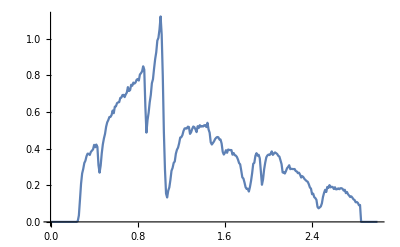

```mathematica
ListPlot[%29,Joined->True]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m1pair4.dat",%29]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m1pair4.dat

```mathematica
LaunchKernels[4]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}